## Analyzing the data

### Importing my databases

```mathematica
SetDirectory[NotebookDirectory[]];
Get["Database\\fullDataset.mx"];
```

### arXives and colors

```mathematica
arXives=DeleteDuplicates[fullDataset[All,"Type"]]//Normal;
colorAssoc[scheme_:"BrightBands"]:=AssociationThread[#,(ColorData[scheme]/@Range[0,1,Length[Rest@#]^-1])]&@arXives;
```

### Normalizer function

```mathematica
normalizer[triple:{_,_,_}]/;triple[[2]]≠0:={triple[[1]],triple[[2]]/triple[[3]]//N};
normalizer[triple:{_,_,_}]/;triple[[2]]==0:={triple[[1]],0};
normalizer[list:{{_,_,_}..}]:=normalizer[#]&/@list;
```

### All arXives

```mathematica
monthfreqData[yearmonthObject_,symbol_]:=Module[{data},data=fullDataset[Select[#YearMonth===yearmonthObject&],"Symbols"];{yearmonthObject,(Merge[data,Total][symbol])/.{_Missing->0},Length[data]}];
rangefreqData[startmonthObject_,endmonthObject_,symbol_]:=monthfreqData[#,symbol]&/@DateRange[startmonthObject,endmonthObject];
```

### By arXiv

```mathematica
monthfreqDatabyarXiv[yearmonthObject_,arXiv_,symbol_]:=Module[{data},data=fullDataset[Select[#YearMonth===yearmonthObject&&#Type==arXiv&],"Symbols"];{yearmonthObject,(Merge[data,Total][symbol])/.{_Missing->0},Length[data]}];
rangefreqDatabyarXiv[startmonthObject_,endmonthObject_,arXiv_,symbol_]:=monthfreqDatabyarXiv[#,arXiv,symbol]&/@DateRange[startmonthObject,endmonthObject];
```

### Frequent symbols

```mathematica
mostFrequentSymbols[firstn_]:=Normal[GroupBy[fullDataset,"Type"][All,All,-1][All,Keys][All,Flatten][All,Counts][All,Sort][All,Reverse][All,Keys][All,StringJoin][All,StringTake[#,firstn]&]];
```

### Clustering Tree

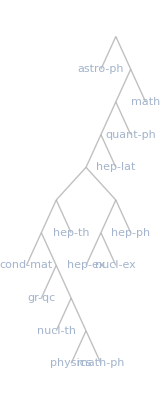

```mathematica
ClusteringTree[mostFrequentSymbols[40]]
```

### Plots

#### Useful functions for plotting

```mathematica
collapse[list_]:={First@First@list,Total/@Rest@Transpose[list]}//Flatten;
reorientData[list_,months_]:=collapse/@Partition[list,months,months,{1,1},{}];
```

#### Plotting functions

```mathematica
plotfreqData[startmonthObject_,endmonthObject_,arXiv_,symbol_:"α",monthbin_:1,scheme_:"Rainbow"]:=DateListStepPlot[normalizer[reorientData[rangefreqDatabyarXiv[startmonthObject,endmonthObject,arXiv,symbol],monthbin]],PlotRange->{All,{0,All}},PlotRangePadding->{None,Automatic},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],PlotStyle->colorAssoc[scheme][arXiv],PlotLabel->Style[arXiv,15],FrameLabel->{Style["Time",15],Style["Frequency",15]}];
```

#### Plots

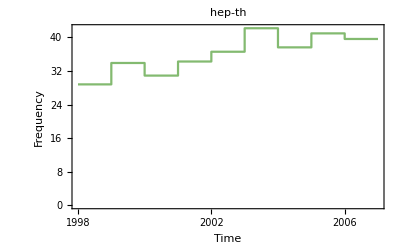

```mathematica
plotfreqData[DateObject[{1998,1}],DateObject[{2006,12}],"hep-th","α",12]
```

### Dendrogram

```mathematica
d[arXiv_]:=Dendrogram[Merge[fullDataset[Select[#Type==arXiv&],"Symbols"]//Normal,Total]];
```

```mathematica
ParallelMap[d,arXives]
```

### Word Clouds

```mathematica
arXivCloud[arxiv_]:=WordCloud[Merge[fullDataset[Select[#Type==arxiv&]][All,"Symbols"]//Normal,Total],PlotLabel->Style[arxiv,30]];
SetAttributes[arXivCloud,Listable];
```

```mathematica
cloudTable=arXivCloud@arXives;
```

```mathematica
imageTable=Image[cloudTable,ImageSize->{360,396}];
DumpSave["output\\images.mx",imageTable];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["output\\images.mx"];
```

```mathematica
blankImage=Image[ConstantArray[1,{198,360}]];
```

```mathematica
image1=ImageAssemble[{#}&/@Flatten[{blankImage,imageTable⟦;;2⟧,blankImage}]];
image2=ImageAssemble[Partition[imageTable⟦3;;11⟧,3]];
image3=ImageAssemble[{#}&/@Flatten[{blankImage,imageTable⟦12;;⟧,blankImage}]];
```

```mathematica
image=ImageAssemble[{image1,image2,image3}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["output\\WCImages.jpg",-Graphics-]
```